This notebook contains a simulation of a controlled inverted pendulum on a cart.

Import dependencies

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
<<draw_inverted_pendulum.m
```

Define constants

```mathematica
(* Acceleration due to gravity in m/s^2 *)
g=9.8;
```

```mathematica
(* The length of the pendulum in m *)
l=0.43;
```

```mathematica
(* The mass of the pendulum in kg *)
m=0.066;
```

```mathematica
(* The mass of the cart in kg *)
M=0.103;
```

```mathematica
(* The duration of the simulation in s *)
tMax=10;
```

Define initial conditions

```mathematica
(* The initial angle of the pendulum in rad *)
θ0=Pi/9;
```

```mathematica
(* The initial angular velocity of the pendulum in rad/s *)
ω0=0;
```

```mathematica
(* The initial x position of the cart in m *)
x0=0;
```

```mathematica
(* The initial x velocity of the cart in m/s *)
v0=0;
```

Define the state, input, state cost, and input cost matrices

```mathematica
(* The state matrix *)
a={
{0, 1, 0, 0},
{g(m+M)/(l M), 0, 0, 0},
{0,0,0,1},
{g m/M,0,0,0}
};
```

```mathematica
(* The input matrix *)
b={
{0},
{1/(l M)},
{0},
{1/M}
};
```

```mathematica
(* The state cost matrix *)
q = {
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
```

```mathematica
(* The input cost matrix *)
r ={{0.01}};
```

Determine the ideal state feedback matrix via the linear quadratic regulator algorithm

```mathematica
(* The state feedback matrix *)
k=LQRegulatorGains[
StateSpaceModel[{a, b, ConstantArray[0,{4,4}],ConstantArray[0,{4,1}]}],
{q,r}
];
```

Generate an animation

```mathematica
Animate[
Module[
{θ,ω,x,v},
{{θ},{ω},{x},{v}}=MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}};
drawInvertedPendulum[l,θ,x]
],
{t,0,tMax},
DefaultDuration->tMax
]
```

Graph the force over time

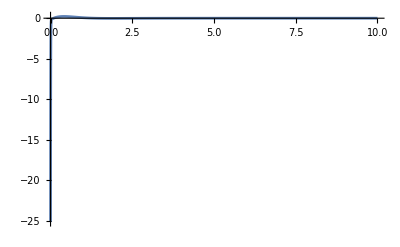

```mathematica
Plot[-k.MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}},{t,0,10},PlotRange->Full]
```

Uncomment to export a GIF of the animation

```mathematica
(* Export[
FileNameJoin[{NotebookDirectory[],"controlled.gif"}],
Table[
Module[
{θ,ω,x,v},
{{θ},{ω},{x},{v}}=MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}};
drawInvertedPendulum[l, θ,x]
],
{t,0,tMax,1/24}
],
DisplayDurations->1/24
]; *)
```